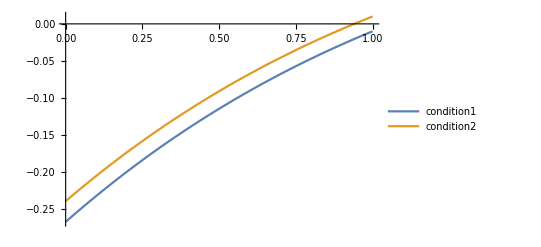

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
(*21.6*)
x0 = 2;
y0 =2;
U1 =5;
U2 = 5;
tf = 1;
t0 = 0;
α = 0.01;
r1 = 1/3;
r2 = 1/2;
d = 1;
p1 = Exp[Integrate[r1, {x, t, tf}]];
p2 = Exp[Integrate[r2, {x, t, tf}]];
condition1 = (1 - α)*p1 - p2;
condition2 = (1 +α)*p1 - p2;
Plot[{condition1, condition2}, {t, 0, tf}, PlotLegends->"Expressions"]
Solve[condition2 == 0, t][[1]][[1]];
u1 = 0;
u2 = 5;
x1star = DSolve[{x'[t]==r1*x[t]-d +(u1 - u2) - α*(u1 + u2), x[0]==x0} , x[t], t][[1]][[1]];
y1star = DSolve[{y'[t] ==r2*y[t]-(u1 - u2), y[0]==y0}, y[t], t][[1]][[1]];
y0star = 9.20279146424349;
t2star = 0.9402980148809911;
x0star = -3.945030551063959;
u1 = 0;
u2 = 0;
x2star =  DSolve[{x'[t]==r1*x[t]-d +(u1 - u2) - α*(u1 + u2),x[t2star]==x0star} , x[t], t][[1]][[1]];
y2star =DSolve[{y'[t] ==r2*y[t]-(u1 - u2), y[t2star]==y0star}, y[t], t][[1]][[1]];
```

ⅇ^((1-t)/3)

ⅇ^(1/2 (1-t) t)

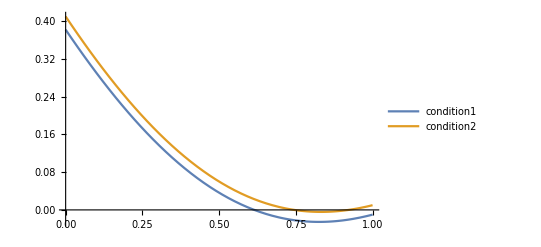

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.614522},{t→1.05214}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.74458},{t→0.922086}}

```mathematica
(*21.7*)
x0 = 2;
y0 =2;
U1 =5;
U2 = 5;
tf = 1;
t0 = 0;
α = 0.01;
r1 = 1/3;
r2 = t/2;
p1 = Exp[Integrate[r1, {x, t, tf}]]
p2 = Exp[Integrate[r2, {x, t, tf}]]
condition1 = (1 - α)*p1 - p2;
condition2 = (1 +α)*p1 - p2;
Plot[{condition1, condition2}, {t, 0, tf}, PlotLegends->"Expressions"]
Solve[condition1 == 0, t]
Solve[condition2 == 0, t]
```